```mathematica
rate[δ_]:=Module[{delta=δ},
(*******************)
(* Free Parameters *)
(*******************)
mx=1 10^3; (* GeV *)
Z=54; (* Atomic Number (Xenon) *)
A=131.904144; (* Atomic Mass (Xenon) *)
a=132;
mN=A 0.93149432; (* Nuclear Mass [GeV] (Xenon) *)


(********************)
(* Fixed Parameters *)
(********************)
mn=0.939;(* Neutron Mass [GeV] *)
rhox=0.3; (* Gev/cm^3 *)
nx=rhox/mx; (* cm^-3 *)
muN=(mx mN)/(mx+mN);(* GeV *)
mun=(mx mn)/(mx+mn); (* GeV *)
Nt=1/mN;(* GeV^-1 *)
fn=1;
fp=1;


(*************************)
(* Velocity Distribution *)
(*************************)
light=2.99792458 10^5;(* km/s *)
v0=220(*km/s*); 
vE=232(*km/s*);
vesc=533(*km/s*); 
vmin[delta_,Er_]:=1/(√(2 Er mN))((Er mN)/muN+delta)light; (* km/s *) (* [delta]=[Er]=GeV *) 
norm=π^(3/2)v0^3(Erf[vesc/v0] -(2 vesc)/(π^(1/2)v0)ⅇ^(-vesc^2/v0^2));  (* (km/s)^3 *)
VelDist[v_,θ_]:=(ⅇ^(-(v^2+vE^2+2 v vE θ)/v0^2))/norm;   (* (km/s)^-3 *)


(****************************)
(* Scattering Cross Section *)
(****************************)
q[Er_]:=√(2 Er  mN);(* GeV *) (* [Er]=GeV *)
b=√(mn^-1 10^3(45 a^(-1/3)-25 a^(-2/3))^-1); (* GeV^-1 *)
u[Er_]:=q[Er]^2 b^2/2; 
c1=-132.841;
c2=38.4859;
c3=-4.08455;
c4=0.153298;
c5=-0.0013897;
F[Er_]:=√(ⅇ^(-u[Er])/a^2(a+c1 u[Er]+c2 u[Er]^2+c3 u[Er]^3+c4 u[Er]^4+c5 u[Er]^5)^2); 
scat[v_,Er_]:=1/(v/light)^2 mN/(2 mun^2)(Z fp + (A-Z)fn)^2/fn^2 F[Er]^2; (* 1/Subscript[σ, 0] dσ/dEr GeV^-1 *)(* [sigma]=cm^2 *) 


(*******************)
(* Scattering Rate *)
(*******************) 
If[delta≤ 14 10^-6,
func1[v_]=Integrate[VelDist[v,θ],{θ,-1,1}];
func2[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}];
rateEnergy[Er_]=   2π nx Nt(10^5) (Integrate[v^3 scat[v,Er]func1[v],{v,vmin[delta,Er],vesc-vE}]+Integrate[v^3 scat[v,Er]func2[v],{v,vesc-vE,vesc+vE}]);  (* s^-1 GeV^-2 cm^-2 *)
Return[NIntegrate[rateEnergy[Er],{Er,1 10^-6,30 10^-6}]](* s^-1 GeV^-1 cm^-2 *)
];
If[14 10^-6<delta≤ 38 10^-6,
Er1=Solve[vmin[delta,Er]==vesc-vE,Er][[1]];
func3[v_]=Integrate[VelDist[v,θ],{θ,-1,1}];
func4[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}];
rateEnergy1[Er_]=   2π nx Nt(10^5) (Integrate[v^3 scat[v,Er]func3[v],{v,vmin[delta,Er],vesc-vE}]+Integrate[v^3 scat[v,Er]func4[v],{v,vesc-vE,vesc+vE}]);  (* s^-1 GeV^-2 cm^-2 *)
rateEnergy2[Er_]=   2π nx Nt(10^5)Integrate[v^3 func4[v]scat[v,Er],{v,vmin[delta,Er],vesc+vE}];(* s^-1 GeV^-2 cm^-2 *)
Return[NIntegrate[rateEnergy1[Er],{Er,Er/.Er1 ,30 10^-6}]+NIntegrate[rateEnergy2[Er],{Er,1 10^-6,Er/.Er1 }]](* s^-1 GeV^-1 cm^-2 *)
];
If[38 10^-6<delta<53 10^-6,
Er2=Solve[vmin[delta,Er]==vesc+vE,Er][[1]];
Er3=Solve[vmin[delta,Er]==vesc-vE,Er][[1]];
func5[v_]=Integrate[VelDist[v,θ],{θ,-1,1}];
func6[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}];
rateEnergy3[Er_]= 2 π nx Nt(10^5) (Integrate[v^3 scat[v,Er]func5[v],{v,vmin[delta,Er],vesc-vE}]+Integrate[v^3 scat[v,Er]func6[v],{v,vesc-vE,vesc+vE}]);  (* s^-1 GeV^-2 cm^-2 *)
rateEnergy4[Er_]= 2π nx Nt(10^5)Integrate[v^3 func6[v]scat[v,Er],{v,vmin[delta,Er],vesc+vE}];(* s^-1 GeV^-2 cm^-2 *)
Return[NIntegrate[rateEnergy3[Er],{Er,Er/.Er3 ,30 10^-6}]+NIntegrate[rateEnergy4[Er],{Er,Er/.Er2 ,(Er/.Er3 )+ 0.00001 10^-6}]](* s^-1 GeV^-1 cm^-2 *)
];
If[delta≥ 53 10^-6,
Er0=Solve[vmin[delta,Er]==vesc+vE,Er][[1]];
func[v_]=Integrate[VelDist[v,θ],{θ,-1,(vesc^2-v^2-vE^2)/(2 vE v)}]; 
rateEnergy7[Er_]= 2π nx Nt(10^5)Integrate[v^3 func[v]scat[v,Er],{v,vmin[delta,Er],vesc+vE}];(* s^-1 GeV^-2 cm^-2 *)
Return[NIntegrate[rateEnergy7[Er],{Er,Er/.Er0 ,30 10^-6}]](* s^-1 GeV^-1 cm^-2 *)
];
](* R/Subscript[σ, 0] s^-1 GeV-1 cm^-2*)
```

```mathematica
(*******************************)
(* Velocity Integral condition *)
(*******************************)
(* delta > ~ 53 10^-6 then vmin never < vesc-vE *)
(* delta < ~ 14 10^-6 then vmin is always < vesc-vE *)
(* 38 ~ < delta < ~ 53 vmin may be larger than vesc+vE *)
par=185 10^-6;
Reduce[vmin[par,Er]< vesc-vE&& 1 10^-6≤ Er≤ 30 10^-6,Er,Reals]
Reduce[vmin[par,Er]> vesc+vE&& 1 10^-6≤ Er≤ 30 10^-6,Er,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

False

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

1.×10^-6≤Er<0.000029838

```mathematica
(*********************)
(* Experimental Data *)
(*********************)
26114463112166000000;(* GeV/tonne *)
24 60 60 ;(* s/day *)
const=3.9(* event *)/(47 (* tonne - day *)26114463112166000000(* GeV/tonne *)24 60 60 (* s/day *))(* s^-1 GeV^-1 *)
```

3.67766×10^-26

```mathematica
(***********)
(* scaling *)
(***********)
scaling=(2 10^-45 rate[0])/const;
```

```mathematica
(******************)
(* sigma vs delta *)
(******************)
sigma[δ_]:=scaling const/rate[δ] ;
```

```mathematica
sigmadata=Table[{i 10^6 ,sigma[i ]},{i,0 10^-6 ,185 10^-6 ,(185  10^-6)/370}];
sigmadata2=Append[sigmadata,{185.41 ,sigma[185.41 10^-6]}];
sigmafunc=Interpolation[sigmadata2,InterpolationOrder->1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Er near {Er} = {0.0000299999}. NIntegrate obtained 5.76394×10^-10 and 3.47169×10^-14 for the integral and error estimates.

InterpolatingFunction[…]

```mathematica
(*****************************)
(* Digitized Plot for Check *)
(*****************************)
checkdata={{2.571 10^-1 ,2.037 10^-45},
{6.491 10^0 ,2.178 10^-45},
{1.720 10^1 ,2.737 10^-45},
{2.792 10^1 ,3.837 10^-45},
{3.863 10^1 ,5.694 10^-45},
{4.934 10^1 ,8.926 10^-45},
{6.006 10^1 ,1.449 10^-44},
{7.077 10^1 ,2.291 10^-44},
{8.141 10^1 ,3.903 10^-44},
{9.171 10^1 ,7.631 10^-44},
{1.015 10^2 ,1.372 10^-43},
{1.108 10^2 ,2.484 10^-43},
{1.185 10^2 ,4.491 10^-43},
{1.268 10^2 ,8.053 10^-43},
{1.341 10^2 ,1.567 10^-42},
{1.419 10^2 ,3.054 10^-42},
{1.489 10^2 ,6.113 10^-42},
{1.540 10^2 ,1.160 10^-41},
{1.598 10^2 ,2.746 10^-41},
{1.649 10^2 ,5.927 10^-41},
{1.687 10^2 ,1.150 10^-40},
{1.711 10^2 ,1.985 10^-40},
{1.732 10^2 ,3.803 10^-40},
{1.755 10^2 ,7.168 10^-40},
{1.778 10^2 ,1.762 10^-39},
{1.799 10^2 ,3.692 10^-39},
{1.804 10^2 ,6.552 10^-39},
{1.809 10^2 ,1.265 10^-36},
{1.814 10^2 ,4.330 10^-35},
{1.815 10^2 ,5.287 10^-34},
{1.817 10^2 ,9.083 10^-34}};
check=Interpolation[checkdata,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
tPowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}]},{i,min10,max10},{k,9}],1]]];
```

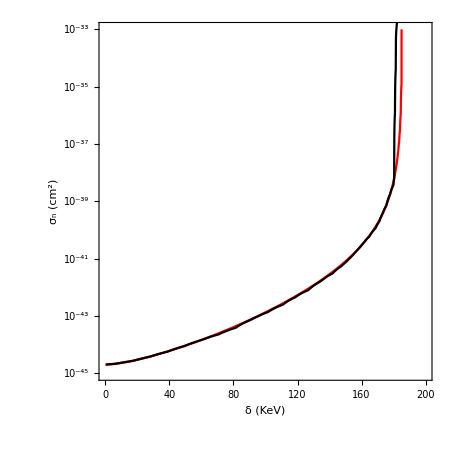

```mathematica
Show[LogPlot[sigmafunc[δ],{δ,0,185.41 },PlotStyle->{Red},PlotRange-> {{ 0 ,200 },{10^-45,10^-33}},FrameTicks-> {{tPowerTicks[True][10^-4, 10^3],Automatic}}],LogPlot[check[δ],{δ,2.571 10^-1 ,2 10^2  },PlotStyle->{Black}],Frame-> True,AspectRatio-> 1,FrameLabel-> { "δ (KeV)","σ_n (cm^2)"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 450]
```